error= 1.237×10^-3

(0.0625 | 0.001237
0.1875 | 0.00117736
0.3125 | 0.00110567
0.4375 | 0.00103451
0.5625 | 0.000964966
0.6875 | 0.000897125
0.8125 | 0.000830811
0.9375 | 0.000765759)

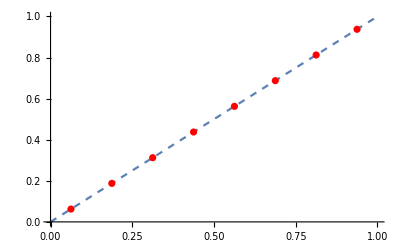

```mathematica
Remove["Global`*"];
H[XX_]:=Module[{xx=XX},
Subscript[h, 1][xx_]=Piecewise[{{1,0≤ xx<1}}];
For[j=0,j≤ J,j++,
For[k=0,k≤ 2^j-1,k++,
Subscript[h, 2^j+k+1][xx_]=Piecewise[{{1,k/2^j≤ xx<(k+0.5)/2^j},{-1,(k+0.5)/2^j≤ xx≤ (k+1)/2^j}},0];
];
];
];
(*****************************************)
K[x_,t_]=Sin[x-t]+1;
g[t_]=(t Sin[t])/2+Sin[t];
yReal[t_]=t;
a=0;
(*****************************************)
M=4;J=2;
AA=Table[Subscript[aa, i],{i,2M}];
KK[x_,t_]=N[D[K[x,t],x]/K[x,x],20];
gp1[x_]=N[D[g[x],x]/K[x,x],20];
For[l=1,l≤ 2M,l++,Subscript[𝓍, l]=(l-0.5)/(2 M)];
H[x];
ℐ=ParallelTable[∫_a^Subscript[𝓍, l] KK[Subscript[𝓍, l],t]Subscript[h, i][t]ⅆt,{i,2M},{l,2M}];
Ans=ParallelTable[∑_(i=1)^(2M) Subscript[aa, i](Subscript[h, i][Subscript[𝓍, l]]+ℐ⟦i,l⟧)-gp1[Subscript[𝓍, l]],{l,1,2M}];
AA=Flatten[AA/.Solve[Ans==0,AA]];
w[t_]=Simplify[∑_(i=1)^(2M) AA⟦i⟧Subscript[h, i][t]];
Subscript[yt, J][t_]=ArcCos[w[t]];
error=Table[Abs[Subscript[yt, J][Subscript[𝓍, l]]-yReal[Subscript[𝓍, l]]],{l,1,2M}];

Subscript[MAE, J]=Max[error];
Print["error= ",ScientificForm[Subscript[MAE, J]]];
Print[MatrixForm[Table[{Subscript[𝓍, l],error⟦l⟧},{l,1,2M}]]]
Show[Plot[yReal[t],{t,0,1},PlotStyle->{Dashed}],ListPlot[Table[{Subscript[𝓍, l],yReal[Subscript[𝓍, l]]},{l,1,2M}],PlotStyle->{Red}]]
```

```mathematica
Subscript[yt, J][t]//Simplify
```

ArcCos[Piecewise[{{-0.250019, t==1.}, {0., t>1.||t<0}, {0.592422, 0.875≤t<1.}, {0.651771, t==0.75}, {0.688289, 0.75<t<0.875}, {0.773404, 0.625≤t<0.75}, {0.792946, t==0.5}, {0.846439, 0.5<t<0.625}, {0.906251, 0.375≤t<0.5}, {0.944191, t==0.25}, {0.951907, 0.25<t<0.375}, {0.982692, 0.125≤t<0.25}, {0.998124, True}}]]